\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Introduction to Mathematica (MMA) -- 02

Zu-Cheng Chen

Institute of Theoretical Physics, 
Chinese Academy of Sciences

@ Guangzhou University, Jul 2019

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## List

## Create lists

```mathematica
a={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
b={{x1,x2},{y1,y2}}
%//MatrixForm
```

{{x1,x2},{y1,y2}}

(x1 | x2
y1 | y2)

```mathematica
Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
c=Table[f[i]+f[j],{i,1,3},{j,1,3}]
c//MatrixForm
```

{{2 f[1],f[1]+f[2],f[1]+f[3]},{f[1]+f[2],2 f[2],f[2]+f[3]},{f[1]+f[3],f[2]+f[3],2 f[3]}}

(2 f[1] | f[1]+f[2] | f[1]+f[3]
f[1]+f[2] | 2 f[2] | f[2]+f[3]
f[1]+f[3] | f[2]+f[3] | 2 f[3])

## Access elements

```mathematica
c[[1]]
```

{2 f[1],f[1]+f[2],f[1]+f[3]}

```mathematica
c[[1]][[1]]
```

2 f[1]

```mathematica
c[[1,1]]
```

2 f[1]

## Map

```mathematica
Clear[a,b,c]
list={a,b,c}
f/@list
```

{a,b,c}

{f[a],f[b],f[c]}

```mathematica
Table[f[i],{i,list}]
```

{f[a],f[b],f[c]}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Everything in MMA is an expression!

## Head

```mathematica
c=a+b
c//Head
```

a+b

Plus

```mathematica
Plus[a,b]
```

a+b

```mathematica
d=f[x+b[y],z*m]
```

f[x+b[y],m z]

```mathematica
d[[0]]
```

f

```mathematica
d[[1]]
```

x+b[y]

## Replace head: @@

```mathematica
c=a+b
f@@c
```

a+b

f[a,b]

```mathematica
d={a,b}
f@@d
```

{a,b}

f[a,b]

## Map

```mathematica
expr=x+y+z+u
Log/@expr
```

u+x+y+z

Log[u]+Log[x]+Log[y]+Log[z]

## FullForm

```mathematica
d//FullForm
```

f[Plus[x,b[y]],Times[m,z]]

## TreeForm

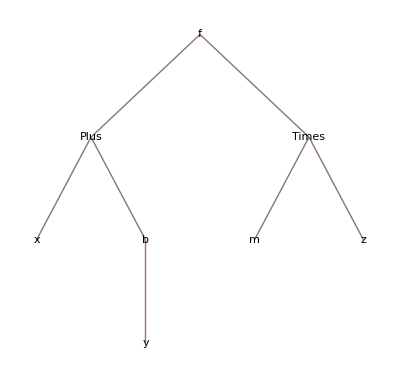

```mathematica
d//TreeForm
```

## Exercise

Consider the following expression:
G[p,q][x,y,z]

How can you access the element q ?

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Rules

## _ : stands for any Wolfram Language expression

```mathematica
rule01=f[x_]->x^2
```

f[x_]→x^2

```mathematica
f[3]
```

f[3]

```mathematica
f[3]/.rule01
```

9

```mathematica
rule02=f[x_]:>x^2
```

f[x_]:>x^2

```mathematica
f[3]/.rule02
```

9

## __ : stands for any sequence of one or more Wolfram Language expressions

```mathematica
rule03=f[x__]:>Plus@x
```

f[x__]:>+x

```mathematica
f[a,b]
```

f[a,b]

```mathematica
f[a,b]/.rule03
```

a+b

## ___ : stands for any sequence of zero or more Wolfram Language expressions

```mathematica
rule04=f[x___]:>Plus@x
```

f[x___]:>+x

```mathematica
f[a,b]
f[a,b]/.rule04
```

f[a,b]

a+b

```mathematica
f[]
f[]/.rule04
```

f[]

0

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Pure function

```mathematica
f1[x_]:=x^2
```

```mathematica
f2=Function[x,x^2]
f2[y]
```

Function[x,x^2]

y^2

```mathematica
f3=Function[#^2]
f3[y]
```

#1^2&

y^2

```mathematica
f4=#^2&
f4[y]
```

#1^2&

y^2

```mathematica
Sin[5]//N
```

-0.958924

```mathematica
N[Sin[5],10]
```

-0.9589242747

```mathematica
Sin[5]//N[#,10]&
```

-0.9589242747

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Module -- local variable

```mathematica
a=3;
g[x_]:=Module[
{a},
a=x^2+1;
Print[a]
]
```

```mathematica
g[3]
```

10

```mathematica
a
```

3

## Exercise

Rewrite S_n function using Module.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Visualization

## Plot

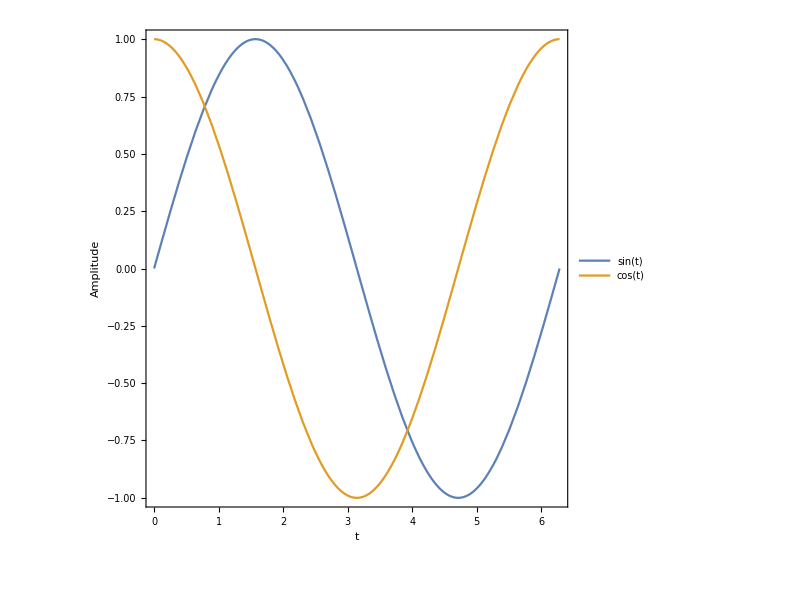

```mathematica
Plot[{Sin[t],Cos[t]},{t,0,2*π},Frame->True,PlotLegends->"Expressions",FrameLabel->{"t","Amplitude"},BaseStyle->Large,ImageSize->600,AspectRatio->1]
```

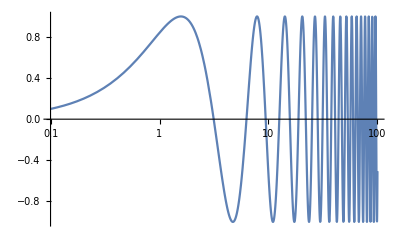

```mathematica
LogLinearPlot[Sin[x],{x,10^-1,10^2},PlotRange->All]
```

```mathematica
Plot3D[Sin[x]*Cos[y],{x,0,2*π},{y,0,2*π},AxesLabel->Automatic]
```

-Graphics3D-

## ListPlot

```mathematica
data=Table[{x,Sin[x]},{x,0,2*π,0.1}];
```

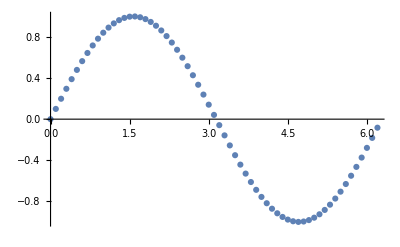

```mathematica
ListPlot[data]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Parallel

```mathematica
Clear@f;
f[x_?NumericQ]:=NIntegrate[x*Sin[y+x]*Cos[y],{y,1,10}]
```

```mathematica
f[1]//AbsoluteTiming
```

{0.047341,3.67605}

```mathematica
LaunchKernels[8]
```

{KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

```mathematica
xs=Range[2*10^3];
```

```mathematica
f/@xs;//AbsoluteTiming
```

{0.635548,Null}

```mathematica
Map[f,xs];//AbsoluteTiming
```

{0.647017,Null}

```mathematica
Distribute@f;
```

```mathematica
(ParallelMap[f,xs]);//AbsoluteTiming
```

{0.262209,Null}

```mathematica
(data=ParallelTable[{x,f[x]},{x,xs}];)//AbsoluteTiming
```

{3.11563,Null}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Import/Export

Create a "backup" directory

```mathematica
SetDirectory[NotebookDirectory[]];

If[Not[DirectoryQ["backup"]],CreateDirectory["backup"]];
```

```mathematica
Export["data.m",data]
```

data.m

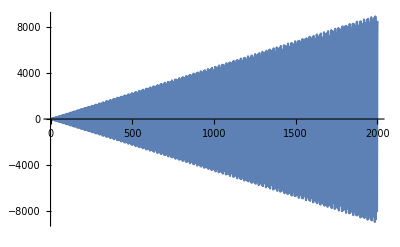

```mathematica
data=Import["data.m"];
ListPlot[data,Joined->True]
```

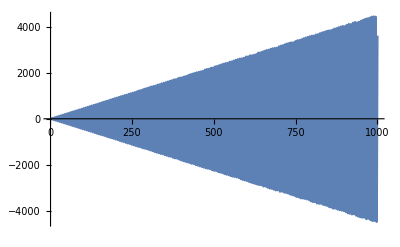
{19.8018,-Graphics-}

```mathematica
Plot[f[x],{x,1,1000}]//AbsoluteTiming
```